```mathematica
color1=RGBColor[0.,0.35294117647058826,0.3686274509803922];
color2=RGBColor[0.,0.45098039215686275,0.4666666666666667];
```

```mathematica
Notebooks[]
```

{a3szq_shm16FrontEndObject[LinkObject["a3szq_shm", 3, 1]]16construction.nbD:\github\vernier\development\construction.nb,a3szq_shm24FrontEndObject[LinkObject["a3szq_shm", 3, 1]]24dual-range-force-sensor.nbD:\github\vernier\basic-usage\dual-range-force-sensor.nb,a3szq_shm1FrontEndObject[LinkObject["a3szq_shm", 3, 1]]1Messages}

```mathematica
SetOptions[a3szq_shm24FrontEndObject[LinkObject["a3szq_shm", 3, 1]]24"dual-range-force-sensor.nb""D:\\github\\vernier\\basic-usage\\dual-range-force-sensor.nb",DockedCells->{
Cell["","DockedCell",Background->color1,CellMargins->0,CellFrameMargins->0,CellFrame->False],
cell}]
```

```mathematica
vernier=ImageCrop[-Graphics-]
```

-Graphics-

```mathematica
cell=Cell[BoxData@ToBoxes@Row[{Image[vernier,ImageSize->{170,65}],Spacer[100],Style["Dual-Range Force Sensor",FontColor->White,FontSize->36,FontWeight->Bold,FontFamily->"Helvetica"]}],"DockedCell",Background->color2,CellMargins->0,CellFrameMargins->15,CellFrame->False]
```

Cell[BoxData[TemplateBox[{GraphicsBox[TagBox[RasterBox[RawArray[UnsignedInteger8,<65,170,3>],{{0,65},{170,0}},{0,255},ColorFunction→RGBColor],BoxForm`ImageTag[Byte,ColorSpace→RGB,Interleaving→True,Magnification→Automatic],Selectable→False],DefaultBaseStyle→ImageGraphics,ImageSizeRaw→{170,65},PlotRange→{{0,170},{0,65}},ImageSize→{170,65}],InterpretationBox[StyleBox[GraphicsBox[{},ImageSize→{100,0},BaselinePosition→Baseline],CacheGraphics→False],,Selectable→False],StyleBox["Dual-Range Force Sensor",FontColor→GrayLevel[1],FontSize→36,FontWeight→Bold,FontFamily→Helvetica,StripOnInput→False]},RowDefault]],DockedCell,Background→RGBColor[0., 0.45098039215686275, 0.4666666666666667],CellMargins→0,CellFrameMargins→15,CellFrame→False]

```mathematica
col1=N@Interpreter["Color"]["#18767A"]
```

RGBColor[0.09411764705882353, 0.4627450980392157, 0.47843137254901963]

```mathematica
col2=N@Interpreter["Color"]["rgb(24,118,122)"]
```

RGBColor[0.09411764705882353, 0.4627450980392157, 0.47843137254901963]

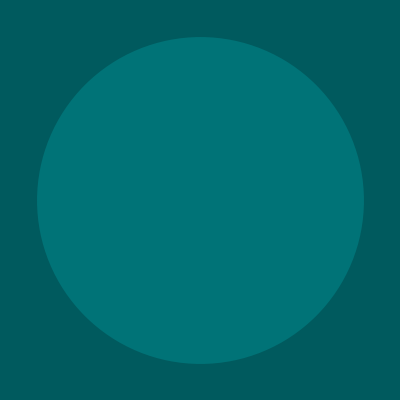

```mathematica
Graphics[{color2,Disk[]},Background->color1]
```

```mathematica
r
```

```mathematica
Options[Cell]
```

{ImportAutoReplacements→{->→→,:>→:>,<=→≤,>=→≥,!=→≠,==→==,<->→<->},ExportAutoReplacements→{→→->,:>→:>,≤→<=,≥→>=,≠→!=,==→==,==→==,
→
,
→
,-→-,⟦→[[,⟧→]],«→<<,»→>>,→ ,→ ,×→*,÷→/,ⅇ→E,ⅈ→I,→,‘→',’→',“→",”→",<|→<|,|>→|>,<->→<->},Default2DTool→Select,Default3DTool→RotateView,CaseSensitiveCommandCompletion→True,EvaluatorNames→{Local→{AutoStartOnLaunch→True},LinkSnooper→{AutoStartOnLaunch→False,MLOpenArguments→-LinkMode Launch -LinkName {oq}`javaw` -classpath {iq}`jlinkjar`{iq} com.wolfram.jlink.util.LinkSnooper -noinit -kernelname {iq}`mathkernel`{iq}{oq}}},FontSubstitutions→{Helvetica→Arial,Courier→Courier New,Times→Times New Roman,Helv→Helvetica,Courier New→Courier,Lucidabright→Times New Roman,Charter→Arial,Lucidatypewriter→Courier,Fixed→Monaco,Gill→Trebuchet MS,Trebuchet MS→Arial,Helvetica Neue→Helvetica,Baskerville→Georgia,Cochin→Constantia,Verdana→Arial,Arial Unicode MS→Lucida Sans Unicode,Lucida Sans Unicode→Arial Unicode MS,Calibri→Arial,Cambria→Times New Roman,Candara→Trebuchet MS,Consolas→Lucida Console,Constantia→Palatino Linotype,Corbel→Lucida Sans,Meiryo→ＭＳ ゴシック,AGaramond→Times New Roman,Avant Garde→Arial,Bodoni→Times New Roman,Bookman→Times New Roman,Caslon 3 Roman→Times New Roman,Caslon 540 Roman→Times New Roman,Century Old Style→Times New Roman,Chicago→Arial,Dom Casual→Arial,Futura→Arial,Futura Book→Arial,Futura Condensed→Arial,C Futura Condensed→Arial,Futura Light→Arial,L Futura Light→Arial,Galliard→Times New Roman,Garamond→Times New Roman,Geneva→Tahoma,GillSans→Gill Sans,Gill Sans→Gill Sans MT,Gill Sans MT→Arial,Goudy→Times New Roman,Helvetica Condensed→Helvetica,C Helvetica Condensed→Helvetica,Helvetica Light→Helvetica,L Helvetica Light→Helvetica,Helvetica Narrow→Helvetica,N Helvetica Narrow→Helvetica,Lucida Grande→Lucida Sans,Lucida Sans→Arial,Melior→Times New Roman,Menlo→Consolas,Meridien→Times New Roman,Mishawaka→Arial,Monaco→Arial,Myriad Pro→Lucida Grande,New Baskerville→Times New Roman,New Century Schlbk→Times New Roman,New York→Times New Roman,Optima→Arial,Palatino→Palatino Linotype,Palatino Linotype→Times New Roman,Prestige Elite→Times New Roman,Sabon→Times New Roman,Tekton→Arial,Trump Mediaeval→Times New Roman,Univers 45 Light→Arial,L Univers 45 Light→Arial,Univers 47 CondensedLight→Arial,CL Univers 47 CondensedLight→Arial,Univers 55→Arial,Univers 57 Condensed→Arial,C Univers 57 Condensed→Arial,Zapf Chancery→Times New Roman,Abadi MT Condensed Light→Arial,Algerian→Times New Roman,Arial Black→Arial,Arial Narrow→Arial,Arial Rounded MT Bold→Arial,Billboard→Arial,Book Antiqua→Times New Roman,Bookman Old Style→Times New Roman,Braggadocio→Arial,Britannic Bold→Arial,Brush Script MT→Arial,Calisto MT→Arial,Century Gothic→Arial,Century Schoolbook→Times New Roman,Colonna MT→Times New Roman,Comic Sans MS→Arial,Desdemona→Arial,Excalibur Logotype→Arial,Excalibur Monospace→Courier,Excalibur Script→Times New Roman,Fixedsys→Arial,Footlight MT Light→Times New Roman,Georgia→Times New Roman,Haettenschweiler→Arial,Impact→Arial,Kino MT→Arial,Kool→Arial,Matura MT Script Capitals→Times New Roman,Modern→Arial,MS LineDraw→Courier,MS Sans Serif→Arial,MS Serif→Times New Roman,News Gothic MT→Arial,Playbill→Arial,Small Fonts→Arial,System→Arial,Wide Latin→Times New Roman,Wingdings→Times New Roman,Gothic→Arial,New century schoolbook→Times New Roman,Swiss721bt→Arial,Terminal→Courier,Utopia→Times New Roman,Frutiger LT Std 55 Roman→Arial,FrutigerLTStd-Light→Arial,Janson Text LT Std→Times New Roman,WriCMTT-Base→Courier,Bitstream Vera Sans→Arial,Bitstream Vera Sans Mono→Consolas,DejaVu Sans Mono→Consolas,Lato→Gill Sans},DefaultFontProperties→{Times→{FontSerifed→True,FontMonospaced→False},Helvetica→{FontSerifed→False,FontMonospaced→False},Courier→{FontSerifed→True,FontMonospaced→True},Symbol→{FontEncoding→Symbol,FontSerifed→True,FontMonospaced→False},ZapfDingbats→{FontEncoding→ZapfDingbats,FontSerifed→True,FontMonospaced→False}},DebuggerSettings→{BreakOnAllMessages→False,BreakOnAsserts→True,BreakpointStyle→{FontColor→RGBColor[1., 0.3, 0.3]},BreakpointsGroup→True,BreakpointsWindowMargins→Automatic,BreakpointsWindowSize→{Automatic,Automatic},DebuggerEnabled→False,EvaluatorPositionHighlightStyle→{Background→RGBColor[0., 0.8, 0., 0.3]},HighlightBreakpoints→True,HighlightEvaluatorPosition→True,HighlightStackFrames→True,MessageBreakpointsGroup→False,ShowBreakpoints→False,ShowStack→False,ShowTools→True,StackHighlightStyle→{FontColor→RGBColor[0., 0.8, 0.]},StackWindowMargins→Automatic,StackWindowSize→{Automatic,Automatic},ToolsWindowMargins→{{Automatic,4},{Automatic,4}},WatchpointsGroup→False},Editable→True,StyleEnvironment→Automatic,ScreenStyleEnvironment→Working,PrintingStyleEnvironment→Printout,Evaluator→Local,Selectable→True,Clickable→True,Deletable→True,PageWidth→WindowWidth,ControlsRendering→Automatic,CellFrame→False,CellDingbat→None,ShowCellBracket→True,ShowSelection→True,ShowGroupOpener→False,WholeCellGroupOpener→False,GroupOpenerInsideFrame→False,ShowClosedCellArea→False,ShowShortBoxForm→False,CellMargins→{{7,3},{4,4}},GroupOpenerColor→GrayLevel[0.49999237048905165],CellBracketOptions→{Color→RGBColor[0.5400015259021896, 0.5539940489814603, 0.7869993133440146],HoverColor→RGBColor[0.5400015259021896, 0.5539940489814603, 0.7869993133440146],Margins→{0,2},OverlapContent→Automatic,Thickness→0.25,Widths→{0,7}},CellElementSpacings→{CellMinHeight→12,ClosedCellHeight→19,ClosedGroupTopMargin→4},PrivateCellOptions→{CellGroupBaseStyle→{},ContentsOpacity→1.,EvaluationUnmatchedStyle→EvaluationUnmatched,InitializationCellStyle→InitializationCell,PagewiseNotebookBaseStyle→{}},Deployed→False,Enabled→True,CellEditDuplicate→False,CellEditDuplicateMakesCopy→False,ReturnCreatesNewCell→False,StyleKeyMapping→{},CellSplitCopiesTags→True,Evaluatable→False,EvaluationMode→Mathematica,Copyable→True,CellOpen→True,CellGroupingRules→NormalGrouping,AllowGroupClose→Automatic,AllowReverseGroupClose→Automatic,ConversionRules→None,TaggingRules→None,CreateCellID→False,TextClipboardType→PlainText,StripStyleOnPaste→False,CellHorizontalScrolling→False,SpeechNavigation→False,SpeechNavigationOptions→{Delete→True,Input→True,Motion→True,Output→True,Parameters→{},Paste→True,Select→True},DataCompression→True,PageBreakAbove→Automatic,PageBreakWithin→Automatic,PageBreakBelow→Automatic,GroupPageBreakWithin→Automatic,OutputSizeLimit→1048576,CellContext→Global`,CellProlog→None,CellEpilog→None,CellEvaluationFunction→Identity,AllowDebugging→True,DynamicUpdating→Automatic,VariableChangesAreEdits→Automatic,MaintainDynamicCaches→False,InitializationCell→False,InitializationGroup→False,CellEvaluationDuplicate→False,GeneratedCell→False,CellAutoOverwrite→False,GenerateImageCachesOnPlacement→False,LegacyGraphicsCompatibility→False,PreserveOldOutputGraphicsAttributes→True,CellEventActions→None,CellDynamicExpression:>Null,DynamicEvaluationTimeout→6.,TemporaryControlActiveInterval→2.,PrivateEvaluationOptions→{OutputFormPageWidth→WindowWidth},GeneratedCellStyles→{Graphics→Graphics,Message→{Message,MSG},Output→Output,Print→Print,PrintTemporary→PrintTemporary},ShowCellLabel→True,CellLabelStyle→CellLabel,CellLabelPositioning→Automatic,CellLabelAutoDelete→True,CellLabelMargins→{{4,0},{2,0}},CellFrameMargins→8,CellFrameColor→GrayLevel[0.],CellFrameStyle→{},CellFrameLabels→{{None,None},{None,None}},CellFrameLabelMargins→3,ShowCellTags→False,CellSize→{Automatic,Automatic},CellBaseline→Baseline,DefaultNewCellStyle→Input,DefaultNewInlineCellStyle→{},DefaultDuplicateCellStyle→Input,DefaultReturnCreatedCellStyle→Automatic,DefaultFormatType→DefaultTextFormatType,DefaultInlineFormatType→DefaultTextInlineFormatType,CommonDefaultFormatTypes→{Input→StandardForm,InputInline→StandardForm,Output→StandardForm,OutputInline→StandardForm,Text→TextForm,TextInline→TraditionalForm},AutoIndent→Automatic,InputAliases→{intt→RowBox[{∫,RowBox[{■,RowBox[{ⅆ,□}]}]}],dintt→RowBox[{SubsuperscriptBox[∫,■,□],RowBox[{□,RowBox[{ⅆ,□}]}]}],sumt→RowBox[{UnderoverscriptBox[∑,RowBox[{■,=,□}],□],□}],prodt→RowBox[{UnderoverscriptBox[∏,RowBox[{■,=,□}],□],□}],dt→RowBox[{SubscriptBox[∂,□], ,■}],ia→TemplateBox[{■},Inactive],cbrt→RadicalBox[■,3,SurdForm→True,MultilineFunction→None],surd→RadicalBox[■,□,SurdForm→True,MultilineFunction→None],ket→TemplateBox[{■},Ket],bra→TemplateBox[{■},Bra],braket→TemplateBox[{■,□},BraKet],delay→TemplateBox[{■},SystemsModelDelay],grad→RowBox[{SubscriptBox[∇,■],□}],del.→RowBox[{SubscriptBox[∇,■],.,□}],delx→RowBox[{SubscriptBox[∇,■],×,□}],del2→RowBox[{SubsuperscriptBox[∇,■,2],□}],kd→TemplateBox[{■},KroneckerDeltaSeq]},InputAutoReplacements→{},ContextMenu→FEPrivate`FrontEndResource[ContextMenus,Text],ComponentwiseContextMenu→{GraphicsBox→FEPrivate`FrontEndResource[ContextMenus,GraphicsBox],Graphics3DBox→FEPrivate`FrontEndResource[ContextMenus,Graphics3DBox],LocatorPaneBox→FEPrivate`FrontEndResource[ContextMenus,LocatorPaneBox],CellGroup→FEPrivate`FrontEndResource[ContextMenus,CellGroup],CellBracket→FEPrivate`FrontEndResource[ContextMenus,CellBracket],CellRange→FEPrivate`FrontEndResource[ContextMenus,CellRange],CellInsertionPoint→FEPrivate`FrontEndResource[ContextMenus,CellInsertionPoint],MisspelledText→FEPrivate`FrontEndResource[ContextMenus,MisspelledText]},CellChangeTimes→{},TrackCellChangeTimes→True,CellChangeTimeMergeInterval→30.,DelimiterFlashTime→0.3,ShowCursorTracker→True,MousePointerAppearance→Automatic,ShowAutoStyles→True,ShowCodeAssist→True,ShowAutoConvert→False,ShowAutoSpellCheck→True,IgnoreSpellCheck→False,ShowMissingStyles→False,ShowPredictiveInterface→True,ShowSyntaxStyles→True,EmphasizeSyntaxErrors→False,StructuredSelection→False,StyleBoxAutoDelete→False,ShowSpecialCharacters→True,AllowInlineCells→True,PasteBoxFormInlineCells→Automatic,TwoByteSyntaxCharacterAutoReplacement→False,CursorTrackerParameters→{9.,0.1,7.,0.02,4.,0.02,2.,0.02},AutoStyleOptions→{CommentStyle→{FontColor→RGBColor[0.27, 0.58, 0.68],ShowAutoStyles→False,ShowSyntaxStyles→False,AutoNumberFormatting→False,TranslationOptions→{Enabled→False},FontWeight→Normal},EmphasizedSyntaxErrorStyle→{FontColor→RGBColor[0.8, 0., 0.],Background→RGBColor[1., 0.88, 0.51]},ExcessArgumentStyle→{FontColor→RGBColor[1., 0.2, 0.2]},FormattingErrorStyle→{FontColor→RGBColor[1., 0.33, 0.33],Background→RGBColor[1., 0.33, 0.33, 0.15]},FormattingErrorTooltips→True,FunctionLocalVariableStyle→{FontColor→RGBColor[0.235, 0.49, 0.568]},GlobalToLocalScopeConflictStyle→{FontColor→RGBColor[0.8, 0., 0.]},GraphicsCompatibilityProblemStyle→{FontColor→RGBColor[1., 0.2, 0.2]},HighlightComments→True,HighlightEmphasizedSyntaxErrors→True,HighlightExcessArguments→True,HighlightFormattingErrors→True,HighlightFunctionLocalVariables→True,HighlightGlobalToLocalScopeConflicts→True,HighlightGraphicsCompatibilityProblems→True,HighlightLocalScopeConflicts→True,HighlightLocalVariables→True,HighlightMissingArguments→True,HighlightMissingArgumentsWithTemplate→False,HighlightMisspelledWords→False,HighlightNoKernelPresent→True,HighlightOrderOfEvaluationConflicts→True,HighlightPatternVariables→True,HighlightStrings→True,HighlightSymbolContexts→True,HighlightSymbolShadowing→True,HighlightSyntaxErrors→True,HighlightUndefinedSymbols→True,HighlightUnknownOptions→True,HighlightUnwantedAssignments→True,LocalScopeConflictStyle→{FontColor→RGBColor[0.8, 0., 0.]},LocalVariableStyle→{FontColor→RGBColor[0.263, 0.537, 0.345]},MissingArgumentStyle→{FontColor→RGBColor[1., 0.2, 0.2]},MissingArgumentTemplateStyle→{FontColor→GrayLevel[0.6],FontSlant→Italic,ShowAutoStyles→False,ShowSyntaxStyles→False,AutoNumberFormatting→False,TranslationOptions→{Enabled→False},FontFamily→Times,FontWeight→Plain},MisspelledWordStyle→{FontColor→RGBColor[0.76, 0.33, 0.8]},NoKernelPresentStyle→{FontColor→RGBColor[0., 0., 0.4]},OrderOfEvaluationConflictStyle→{FontColor→RGBColor[1., 0.2, 0.2]},PatternVariableStyle→{FontColor→RGBColor[0.263, 0.537, 0.345],FontSlant→Italic},StringStyle→{FontColor→GrayLevel[0.4],ShowAutoStyles→False,ShowSyntaxStyles→False,AutoNumberFormatting→False,TranslationOptions→{Enabled→False}},SymbolContextStyles→{System`→{},Global`→{},Automatic→{}},SymbolShadowingStyle→{FontColor→RGBColor[1., 0.2, 0.2]},SyntaxErrorStyle→{FontColor→RGBColor[0.76, 0.33, 0.8]},UndefinedSymbolStyle→{FontColor→RGBColor[0., 0.173, 0.765]},UnknownOptionStyle→{FontColor→RGBColor[1., 0.2, 0.2]},UnwantedAssignmentStyle→{FontColor→RGBColor[1., 0.2, 0.2]}},CodeAssistOptions→{AttachedBrowserEnable→True,AutoConvertEnable→True,AutoPopupDelay→0.,AutoPopupEnable→True,CodeFoldingEnable→False,CompletionParameters→{0.85,0.15,7.,15.,0.,10.,20.,0.,10.,-20.,20.,-25.,-10.,-2.,0.6},DynamicHighlighting→True,FileCompleteEnable→True,FloatingElementDelay→0.3,FloatingElementEnable→True,HeadHighlightStyle→{Background→RGBColor[0.843, 1., 0.628]},IncludedCompletions→{},MatchHighlightStyle→{Background→RGBColor[0.679, 0.937, 0.547]},MatchingAlgorithm→Automatic,MaxContextMatches→5,MaxGlobalMatches→5,MaxPlotThemeMatches→9,MenuBorderColor→GrayLevel[0.9257953765163653],MinimalSize→2,PrimaryHoverColor→RGBColor[0.9101701380941482, 0.6523537041275654, 0.6367284657053482],SecondaryHoverColor→RGBColor[0.9101701380941482, 0.6523537041275654, 0.6367284657053482],StringCompleteEnable→True},UndoOptions→{Enabled→Automatic,MaxLength→∞,MemoryLimit→10000000,RememberEvaluations→True,SpoolDirectory→FrontEnd`FileName[{$TemporaryPrefix}]},TextAlignment→Left,TextJustification→0.,TranslationOptions→{BaseStyle→Translation,ContentEnabled→False,Enabled→True,HighlightStyle→SelectedTranslation,Language→Automatic,Margins→{{5,6},{2,2}}},Hyphenation→False,HyphenationOptions→{HyphenationCharacter→-,HyphenationFreeZone→36,HyphenationMinLengths→{3,3}},TabFilling→None,LineSpacing→{1.,1.,2.},ParagraphSpacing→{0.,0.},ParagraphIndent→0,TabSpacings→{4.},AutoItalicWords→{},AutoStyleWords→{},AutoQuoteCharacters→{"→{“,”},'→{‘,’}},PasteAutoQuoteCharacters→{"→{“,”},'→{‘,’}},LanguageCategory→NaturalLanguage,DefaultNaturalLanguage→Automatic,SpellingOptions→{AlwaysSkip→{SingleCharacterWords,Numbers,WordsWithNumbers,WordsInAllCaps,WordsWithUnderscores,WordsWithInternalCapitals,WordsInURL},AlwaysStop→{UncapitalizedStartOfSentence,RepeatedWords},AutoSpellCheckDelay→0.4,AutoSpellCheckPopupDelay→0.4,MaxSuggestions→3,MisspelledWordStyle→MisspelledWord,WordSplitting→Hyphen},SpellingDictionaries→{CorrectWords→{Teh,Cindie,Strater,Tei,Barnhart,Schultheiss,Mengqi,Gu,Auer},IncorrectWords→{},Suggestions→{}},StyleHints→{CodeFont→Consolas},FormatType→TextForm,AutoSpacing→True,ShowContents→True,ScriptSizeMultipliers→{0.71},ImageSizeMultipliers→{0.5,0.25},ScriptMinSize→4,ScriptBaselineShifts→{Automatic,Automatic},ScriptLevel→0,ShowStringCharacters→False,NumberMarks→False,PrintPrecision→6,AutoNumberFormatting→True,AutoMultiplicationSymbol→True,DigitBlock→{3,5},DigitBlockMinimum→{5,∞},NumberPoint→.,NumberSeparator→ ,NumberMultiplier→×,LimitsPositioningTokens→{∑,∏,∩,∪,⊎,⋀,⋁,lim,max,min,⊕,⊖,⊗,⊙},SingleLetterItalics→False,MultiLetterItalics→False,SingleLetterStyle→None,MultiLetterStyle→None,LowerCaseStyle→None,GreekStyle→None,TraditionalFunctionNotation→False,DelimiterMatching→All,ZeroWidthTimes→False,SpanMinSize→Automatic,SpanMaxSize→Automatic,SpanSymmetric→True,SpanLineThickness→Automatic,SpanCharacterRounding→Automatic,SpanAdjustments→Automatic,LineBreakWithin→Automatic,LineIndent→1.,LineIndentMaxFraction→0.5,LinebreakAdjustments→{0.85,2.,12.,1.,1.},LinebreakSemicolonWeighting→PreferentiallyBreak,CounterIncrements→{},CounterAssignments→{},AspectRatioFixed→True,ImageSize→{350,350},ImageMargins→0,ImageRegion→{{0.,1.},{0.,1.}},SpeedOfTime→1.,AnimationRunning→False,AnimationDisplayTime→0.1,AnimationCycleOffset→0,AnimationCycleRepetitions→∞,RenderingOptions→{3DRenderingEngine→Automatic,3DRenderingMethod→Automatic,DepthPeelingLayers→8,HardwareAntialiasingQuality→1.,LegacyAlphaChannelMethod→False,ShowFrameRateCounter→False},CacheGraphics→Automatic,Antialiasing→Automatic,Lighting→Automatic,ClipPlanes→None,ClipPlanesStyle→Automatic,FillForm→None,AlignmentGuidesEnabled→False,SelectAfterDrawing→True,MenuSortingValue→None,MenuCommandKey→None,StyleMenuListing→Automatic,CounterStyleMenuListing→Automatic,FormatTypeAutoConvert→True,VirtualGroupData→None,FontFamily→Times,FontSize→12,FontWeight→Plain,FontSlant→Plain,FontTracking→Plain,FontVariations→{CapsType→Normal,CompatibilityType→Normal,Outline→False,Shadow→False,StrikeThrough→False,Underlight→None,Underline→False},FontProperties→{AutoSpaceWidth→{0.221,0.439},FontMonospaced→Automatic,FontSerifed→Automatic,ScreenResolution→72},PrivateFontOptions→{FontPostScriptName→Automatic,FontType→Bitmap,IntegerLineheights→False,OperatorSubstitution→False,WindowsUseTrueTypeNames→True},Magnification→1.,FontColor→Automatic,FontOpacity→Automatic,Background→None,ShowInvisibleCharacters→{},AdjustmentBoxOptions→{BaseStyle→{},BoxBaselineShift→0.,BoxMargins→0.,DefaultBaseStyle→{},StripOnInput→True},ErrorBoxOptions→{BaseStyle→{},DefaultBaseStyle→{}},ItemBoxOptions→{Alignment→{},AllowScriptLevelChange→True,Background→Automatic,BaseStyle→{},DefaultBaseStyle→{},DefaultFrameStyle→{},Frame→{},FrameStyle→{},ItemSize→{},StripOnInput→True},DynamicModuleBoxOptions→{ActionFunction:>None,AllowKernelInitialization→True,BaseStyle→{},DefaultBaseStyle→{},Deinitialization:>None,DynamicModuleParent:>None,DynamicModuleValues:>None,Initialization:>None,SynchronousInitialization→True,UndoTrackedVariables:>None,UnsavedVariables:>None,UntrackedVariables:>None,Value→False},FormBoxOptions→{BaseStyle→{},DefaultBaseStyle→{}},FrameBoxOptions→{Alignment→{Automatic,Automatic},Appearance→{Automatic,Framed},Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,BoxExpandable→False,BoxFrame→1.,ContentPadding→True,DefaultBaseStyle→Framed,DefaultFrameStyle→{},Enabled→Automatic,FrameMargins→Automatic,FrameStyle→{},ImageMargins→0.,ImageSize→Automatic,RoundingRadius→{0.,0.},StripOnInput→True},InterpretationBoxOptions→{AutoDelete→False,BaseStyle→{},DefaultBaseStyle→{},DefaultTooltipStyle→TooltipLabel,DeleteWithContents→True,DeletionWarning→False,Editable→False,InterpretationNote→None,SelectWithContents→False,Selectable→Automatic,SyntaxForm→Automatic,Tooltip→None,TooltipDelay→0.,TooltipStyle→{}},NamespaceBoxOptions→{AutoDelete→False,BaseStyle→{},DefaultBaseStyle→{},DefaultTooltipStyle→TooltipLabel,DeleteWithContents→True,DeletionWarning→False,Editable→Automatic,PrivateNames→{},PublicNames→{},SelectWithContents→False,Selectable→Automatic,StripWrapperBoxes→False,SyntaxForm→Automatic,Tooltip→None,TooltipDelay→0.,TooltipStyle→{}},RotationBoxOptions→{BaseStyle→{},BoxRotation→0.,BoxRotationPoint→Automatic,DefaultBaseStyle→{}},TagBoxOptions→{AutoDelete→False,BaseStyle→{},DefaultBaseStyle→{},DefaultTooltipStyle→TooltipLabel,DeleteWithContents→True,DeletionWarning→False,Editable→Automatic,SelectWithContents→False,Selectable→Automatic,StripWrapperBoxes→False,SyntaxForm→Automatic,TagBoxNote→None,Tooltip→None,TooltipDelay→0.,TooltipStyle→{}},TemplateBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},DefaultTooltipStyle→TooltipLabel,DisplayFunction→None,Editable→Automatic,Inactive→False,InactiveStyle→InactiveStyle,InterpretationFunction→Automatic,Selectable→Automatic,SyntaxForm→Automatic,Tooltip→None,TooltipDelay→0.,TooltipStyle→{}},LineBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},VertexColors→None},ConicHullRegionBoxOptions→{BaseStyle→{},DefaultBaseStyle→{}},PointBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},VertexColors→None},LocatorBoxOptions→{Alignment→{Automatic,Automatic},Appearance→{Automatic,Automatic},AutoAction→False,Background→Automatic,BaseStyle→{},ContentPadding→True,ContinuousAction→True,DefaultBaseStyle→{},Enabled→Automatic,FrameMargins→3.,ImageMargins→0.,ImageSize→Automatic,LocatorCentering→False,LocatorRegion→Automatic},PolygonBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},VertexColors→Automatic,VertexTextureCoordinates→Automatic},BezierCurveBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},Method→{},SplineClosed→False,SplineDegree→Automatic},BSplineCurveBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},Method→{},SplineClosed→False,SplineDegree→Automatic,SplineKnots→Automatic,SplineWeights→Automatic},XSplineCurveBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},XSplineWeights→Automatic},JoinedCurveBoxOptions→{BaseStyle→{},CurveClosed→False,DefaultBaseStyle→{},Method→{}},FilledCurveBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},Method→{},VertexTextureCoordinates→None},RectangleBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},RoundingRadius→0.},RasterBoxOptions→{BaseStyle→{},ColorFunction→Automatic,ColorFunctionScaling→True,DefaultBaseStyle→{},ImageEditMode→True},CounterBoxOptions→{BaseStyle→{},CounterFunction:>Identity,DefaultBaseStyle→{}},ValueBoxOptions→{BaseStyle→{},DefaultBaseStyle→{}},OptionValueBoxOptions→{BaseStyle→{},DefaultBaseStyle→{}},ActionMenuBoxOptions→{Alignment→{Automatic,Automatic},Appearance→Automatic,AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,DefaultBaseStyle→ActionMenu,DefaultMenuStyle→ActionMenuLabel,Enabled→Automatic,Evaluator→Automatic,FieldSize→{{0.,50.},{0.,10.}},FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→Automatic,MenuAppearance→Automatic,MenuStyle→{},Method→Preemptive},AnimatorBoxOptions→{Alignment→{Automatic,Automatic},AnimationDirection→Forward,AnimationRate→Automatic,AnimationRepetitions→∞,AnimationRunTime→0.,AnimationRunning→True,AnimationTimeIndex→Automatic,Appearance→{Automatic,Palette},AppearanceElements→{ProgressSlider,StepLeftButton,StepRightButton,PlayPauseButton,FasterSlowerButtons,DirectionButton},AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→True,DefaultBaseStyle→{},DefaultDuration→5.,DisplayAllSteps→False,Enabled→Automatic,Exclusions→{},FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→Automatic,PausedTime→Automatic,RefreshRate→Automatic},ButtonBoxOptions→{Active→True,Alignment→{Automatic,Automatic},Appearance→{Automatic,Palette},AutoAction→False,Background→Automatic,BaseStyle→GenericButton,BaselinePosition→Automatic,ButtonData→Automatic,ButtonFunction:>(FrontEndExecute[{FrontEnd`NotebookApply[FrontEnd`InputNotebook[],#1,Placeholder]}]&),ButtonMargins→3,ButtonMinHeight→1.,ButtonNote→None,ButtonSource→Automatic,ContentPadding→True,DefaultBaseStyle→Button,DefaultTooltipStyle→TooltipLabel,Enabled→Automatic,Evaluator→None,FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→Full,Method→Queued,Tooltip→None,TooltipDelay→0.,TooltipStyle→{}},CheckboxBoxOptions→{Appearance→{Automatic,None},AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→False,DefaultBaseStyle→Checkbox,Enabled→Automatic,ImageMargins→Automatic,Momentary→False},ColorSetterBoxOptions→{Appearance→{Automatic,Palette},AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→True,DefaultBaseStyle→ColorSetter,Enabled→Automatic,ImageMargins→Automatic,ImageSize→Automatic},DynamicBoxOptions→{Appearance→{Automatic,None},AutoAction→False,Background→Automatic,BaseStyle→{},CachedValue:>Null,ContentPadding→True,ContinuousAction→True,DefaultBaseStyle→{},Deinitialization:>None,DestroyAfterEvaluation→False,DisplayFunction:>Identity,Enabled→Automatic,Evaluator→Automatic,ImageSizeCache→Automatic,Initialization:>None,RecursionLimit→256,Selectable→Automatic,ShrinkingDelay→0.,SingleEvaluation→False,SynchronousUpdating→True,TrackedSymbols:>All,UpdateInterval:>∞},DynamicWrapperBoxOptions→{Appearance→{Automatic,None},AutoAction→False,Background→Automatic,BaseStyle→{},CachedValue:>Null,ContinuousAction→True,DefaultBaseStyle→{},Deinitialization:>None,DestroyAfterEvaluation→False,DisplayFunction:>Identity,Enabled→Automatic,Evaluator→Automatic,ImageSizeCache→Automatic,Initialization:>None,RecursionLimit→256,Selectable→Automatic,ShrinkingDelay→0.,SingleEvaluation→False,SynchronousUpdating→True,TrackedSymbols:>All,UpdateInterval:>∞},RefBoxOptions→{Appearance→{Automatic,None},AutoAction→False,Background→Automatic,BaseStyle→{},CachedValue:>Null,ContentPadding→True,ContinuousAction→True,DefaultBaseStyle→{},Deinitialization:>None,DestroyAfterEvaluation→False,DisplayFunction:>Identity,Enabled→Automatic,Evaluator→Automatic,ImageSizeCache→Automatic,Initialization:>None,RecursionLimit→256,Selectable→Automatic,ShrinkingDelay→0.,SingleEvaluation→False,SynchronousUpdating→True,TrackedSymbols:>All,UpdateInterval:>∞},InputFieldBoxOptions→{Alignment→{Automatic,Automatic},Appearance→{Automatic,Automatic},Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→False,DefaultBaseStyle→InputField,DefaultFieldHintStyle→FieldHintStyle,Enabled→Automatic,FieldCompletionFunction→Null,FieldHint→Null,FieldHintStyle→{},FieldMasked→False,FieldSize→Automatic,FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→Automatic,MenuList→Null,ReturnEntersInput→True,TrapEnterKey→False,TrapSelection→True},LocatorPaneBoxOptions→{Alignment→{Automatic,Automatic},Appearance→Automatic,AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→True,DefaultBaseStyle→LocatorPane,Enabled→Automatic,Exclusions→{},FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→Automatic,LocatorAutoCreate→False,TouchscreenAutoZoom→False,UseGraphicsRange→All},ListPickerBoxOptions→{Alignment→{Automatic,Automatic},Appearance→Automatic,AppearanceElements→None,AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→True,DefaultBaseStyle→ListPicker,Enabled→Automatic,FieldSize→{{1.,50.},{1.,10.}},FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→Automatic,ListPickerBoxBackground→None,Multiselection→True,ScrollPosition→{0.,0.},Scrollbars→{Automatic,Automatic},Spacings→Automatic},OpenerBoxOptions→{Appearance→{Automatic,None},AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→False,DefaultBaseStyle→Opener,Enabled→Automatic,ImageMargins→Automatic,Momentary→False},OverlayBoxOptions→{Alignment→{Automatic,Automatic},Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,DefaultBaseStyle→Overlay,FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→Automatic},PaneBoxOptions→{Alignment→{Automatic,Automatic},Appearance→Automatic,AppearanceElements→Automatic,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,DefaultBaseStyle→Pane,Enabled→Automatic,FrameMargins→Automatic,ImageMargins→0,ImageSize→Automatic,ImageSizeAction→Automatic,ScrollPosition→{0.,0.},Scrollbars→False,StripOnInput→False},PanelBoxOptions→{Alignment→{Automatic,Automatic},Appearance→{Automatic,Palette},Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,DefaultBaseStyle→Panel,Enabled→Automatic,FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→Automatic,PanelTitle→None,StripOnInput→False,TitleAlignment→Automatic,TitlePositioning→Top},PaneSelectorBoxOptions→{Alignment→{Automatic,Automatic},AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→True,DefaultBaseStyle→PaneSelector,FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→All,TransitionDirection→Horizontal,TransitionDuration→0.5,TransitionEffect→Automatic},PopupMenuBoxOptions→{Alignment→{Automatic,Automatic},Appearance→Automatic,AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→True,DefaultBaseStyle→PopupMenu,DefaultMenuStyle→PopupMenuLabel,Enabled→Automatic,FieldSize→{{1.,50.},{1.,10.}},FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→All,MenuAppearance→Automatic,MenuStyle→{}},ProgressIndicatorBoxOptions→{Appearance→{Automatic,Palette},AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→True,DefaultBaseStyle→ProgressIndicator,Enabled→Automatic,ImageMargins→Automatic,ImageSize→Automatic},RadioButtonBoxOptions→{Appearance→{Automatic,Automatic},AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→True,DefaultBaseStyle→RadioButton,Enabled→Automatic,ImageMargins→Automatic},SetterBoxOptions→{Alignment→{Automatic,Automatic},Appearance→{Automatic,Automatic},AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→True,DefaultBaseStyle→Setter,Enabled→Automatic,FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→All},SliderBoxOptions→{Appearance→{Automatic,Automatic},AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→True,DefaultBaseStyle→Slider,Enabled→Automatic,Exclusions→{},ImageMargins→Automatic,ImageSize→Automatic},Slider2DBoxOptions→{Appearance→{Automatic,Palette},AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→True,DefaultBaseStyle→Slider2D,Enabled→Automatic,Exclusions→{},ImageMargins→Automatic,ImageSize→Automatic},TabViewBoxOptions→{Alignment→{Automatic,Automatic},Appearance→{Automatic,Palette},AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→True,ControlPlacement→{Automatic,Automatic},DefaultBaseStyle→TabView,DefaultLabelStyle→TabViewLabel,Enabled→Automatic,FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→All,LabelStyle→{}},TableViewBoxOptions→{Alignment→{Automatic,Automatic},AllowedDimensions→Automatic,Appearance→Automatic,AppearanceElements→All,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ColHeadersCollapsed→False,ColSizes→{},ContentPadding→True,DefaultBaseStyle→TableView,Enabled→Automatic,FieldSize→{{1.,5.},{1.,1.}},FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→Automatic,RowHeadersCollapsed→False,RowSizes→{},ScrollPosition→{0.,0.},Scrollbars→{Automatic,Automatic},Spacings→Automatic,TableViewBoxBackground→None,TableViewBoxItemSize→{},TableViewDefaultElement→},TogglerBoxOptions→{Alignment→{Automatic,Automatic},AutoAction→False,Background→Automatic,BaseStyle→{},BaselinePosition→Automatic,ContentPadding→True,ContinuousAction→False,DefaultBaseStyle→Toggler,Enabled→Automatic,FrameMargins→Automatic,ImageMargins→Automatic,ImageSize→All,Momentary→False},TooltipBoxOptions→{Background→Automatic,BaseStyle→Tooltip,DefaultBaseStyle→{},DefaultTooltipStyle→TooltipLabel,StripOnInput→False,TooltipDelay→0.,TooltipStyle→{}},SubsuperscriptBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},MultilineFunction→Automatic},SubscriptBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},MultilineFunction→Automatic},SuperscriptBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},MultilineFunction→Automatic},UnderoverscriptBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},DiacriticalPositioning→Automatic,LimitsPositioning→Automatic,MultilineFunction→Automatic},UnderscriptBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},DiacriticalPositioning→Automatic,LimitsPositioning→Automatic,MultilineFunction→Automatic},OverscriptBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},DiacriticalPositioning→Automatic,LimitsPositioning→Automatic,MultilineFunction→Automatic},RadicalBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},ExponentPosition→{0.2,0.1},MultilineFunction→Automatic,SurdForm→False},SqrtBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},MultilineFunction→Automatic,SurdForm→False},FractionBoxOptions→{AllowScriptLevelChange→True,BaseStyle→{},Beveled→False,DefaultBaseStyle→{},DenominatorAlignment→Center,FractionLine→Automatic,MultilineFunction→Automatic,NumeratorAlignment→Center,Overhang→0.25},GridBoxOptions→{AllowScriptLevelChange→True,AllowedDimensions→Automatic,AutoDelete→True,BaseStyle→{},BaselinePosition→Automatic,DefaultBaseStyle→Grid,DefaultFrameStyle→{},DeleteWithContents→True,Editable→Automatic,FrameStyle→{},GridBoxAlignment→{},GridBoxBackground→{},GridBoxDividers→{},GridBoxFrame→{},GridBoxItemSize→{},GridBoxItemStyle→{},GridBoxSpacings→{},GridDefaultElement→□,GridFrame→False,GridFrameMargins→{{0.4,0.4},{0.5,0.5}},MultilineFunction→None,Selectable→Automatic},MultiscriptBoxOptions→{AutoDelete→True,BaseStyle→{},DefaultBaseStyle→{},DefaultElement→□,DefaultTooltipStyle→TooltipLabel,MultilineFunction→None,PostScriptBoxAlignment→{},PostScriptBoxItemSize→{},PostScriptBoxItemStyle→None,PostScriptBoxSpacings→{},PreScriptBoxAlignment→{},PreScriptBoxItemSize→{},PreScriptBoxItemStyle→None,PreScriptBoxSpacings→{},SyntaxForm→Automatic,Tooltip→None,TooltipDelay→0.,TooltipStyle→{}},GraphicsBoxOptions→{AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→{Automatic,Automatic},AxesStyle→{},Background→None,BaseStyle→{},BaselinePosition→Automatic,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions:>Automatic,DefaultAxesStyle→GraphicsAxes,DefaultBaseStyle→Graphics,DefaultFrameStyle→GraphicsFrame,DefaultFrameTicksStyle→GraphicsFrameTicks,DefaultGridLinesStyle→GraphicsGridLines,DefaultLabelStyle→GraphicsLabel,DefaultTicksStyle→GraphicsTicks,Epilog→{},FormatType→TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImageMarkers→None,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,ImageSizeRules→Automatic,LabelStyle→{},Method→{},PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→{{0.,1.},{0.,1.}},PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}},GraphicsGroupBoxOptions→{BaseStyle→{},ContentSelectable→Automatic,DefaultBaseStyle→{}},GraphicsGroup3DBoxOptions→{BaseStyle→{},ContentSelectable→Automatic,DefaultBaseStyle→{}},GeometricTransformationBoxOptions→{ContentSelectable→Automatic},GeometricTransformation3DBoxOptions→{ContentSelectable→Automatic},GraphicsComplexBoxOptions→{BaseStyle→{},ContentSelectable→Automatic,DefaultBaseStyle→{},Textures→{},VertexColors→Automatic,VertexTextureCoordinates→Automatic},InsetBoxOptions→{Alignment→{Center,Center},Background→None,BaseStyle→{},ContentSelectable→Automatic,DefaultBaseStyle→{},FormatType→Automatic},Graphics3DBoxOptions→{AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaseStyle→{},BaselinePosition→Automatic,BoxRatios→Automatic,BoxStyle→{},Boxed→True,ClipPlanes→None,ClipPlanesStyle→Automatic,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions:>Automatic,DefaultAxesStyle→Graphics3DAxes,DefaultBaseStyle→Graphics3D,DefaultBoxStyle→Graphics3DBox,DefaultFaceGridsStyle→Graphics3DFaceGrids,DefaultLabelStyle→Graphics3DLabel,DefaultTicksStyle→Graphics3DTicks,Epilog→{},FaceGrids→None,FaceGridsStyle→{},FormatType→TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,ImageSizeRules→Automatic,LabelStyle→{},Lighting→Automatic,Method→{CylinderPoints→{40,3},ConePoints→{40,3},SpherePoints→{40,30},TubePoints→{40,2},SplinePoints→7,RotationControl→ArcBall},PlotLabel→None,PlotRange→All,PlotRangePadding→Automatic,PlotRegion→{{0.,1.},{0.,1.}},PreserveImageOptions→Automatic,Prolog→{},RotationAction→Fit,SphericalRegion→False,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0.,0.,1.}},Point3DBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},VertexColors→None,VertexNormals→None},Line3DBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},VertexColors→None,VertexNormals→None},TubeBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},VertexColors→None},TubeBezierCurveBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},Method→{},SplineClosed→False,SplineDegree→Automatic,VertexColors→None},TubeBSplineCurveBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},Method→{},SplineClosed→False,SplineDegree→Automatic,SplineKnots→Automatic,SplineWeights→Automatic,VertexColors→None},Raster3DBoxOptions→{AlphaMask→None,BaseStyle→{},ClipRange→None,ColorFunction→Automatic,DefaultBaseStyle→{},ImageEditMode→True,Method→{InterpolateValues→False},PlotRange→Automatic,PlotRangeClipPlanesStyle→Automatic,VertexDataCoordinates→Automatic},Polygon3DBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},VertexColors→Automatic,VertexNormals→Automatic,VertexTextureCoordinates→Automatic},BezierCurve3DBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},Method→{},SplineClosed→False,SplineDegree→Automatic,VertexColors→None,VertexNormals→None},BSplineCurve3DBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},Method→{},SplineClosed→False,SplineDegree→Automatic,SplineKnots→Automatic,SplineWeights→Automatic,VertexColors→None,VertexNormals→None},BSplineSurface3DBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},Method→{},SplineClosed→False,SplineDegree→Automatic,SplineKnots→Automatic,SplineWeights→Automatic,VertexColors→None,VertexNormals→None},Text3DBoxOptions→{Background→None,BaseStyle→{},DefaultBaseStyle→{},FormatType→Automatic},Inset3DBoxOptions→{Alignment→{Center,Center},Background→None,BaseStyle→{},DefaultBaseStyle→{},FormatType→Automatic,Graphics3DMode→Automatic},ConicHullRegion3DBoxOptions→{BaseStyle→{},DefaultBaseStyle→{}},GraphicsComplex3DBoxOptions→{BaseStyle→{},ContentSelectable→Automatic,DefaultBaseStyle→{},Textures→{},VertexColors→Automatic,VertexNormals→Automatic,VertexTextureCoordinates→Automatic},HexahedronBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},VertexColors→None,VertexTextureCoordinates→None},PrismBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},VertexColors→None,VertexTextureCoordinates→None},PyramidBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},VertexColors→None,VertexTextureCoordinates→None},TetrahedronBoxOptions→{BaseStyle→{},DefaultBaseStyle→{},VertexColors→None,VertexTextureCoordinates→None},CellLabel→None,Name→None,GroupName→None,CellTags→{},CellID→None,ExpressionUUID→None}